(-2+1/(√2)) (-1/(√2)-y)

{-x y-y (-x-x y),(2-x) y+(-2-y) (-x-x y)}

$Aborted

(x==0||x==1)&&y==x

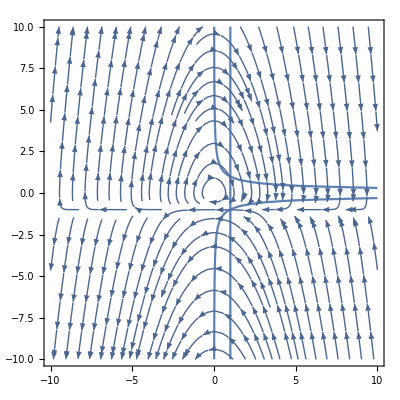

```mathematica
vf=-{x*y^3,x+y};
vf=-{-y,x+x*y};
vars={x,y};
g=2*x+x*y;
g=-7 (2-x);
g={(-2+1/(√2)) (-1/(√2)-y),(-2-1/(√2)) (1/(√2)-y)}[[1]]
Clear[p];
Clear[Lfp];
SplitVariety[p_?PolynomialQ,variables_List,vectorField_List]:=Module[{},
Lfp=Grad[p,variables].vectorField;
NonSingular=Not[Apply[And, Map[Apply[Equal,#]&,Transpose[{Grad[p,variables],Map[0*#&,variables]}]]]];
Pts=FindInstance[p==0 && Lfp==0 &&NonSingular,variables,Reals,5];
(*OrthL=Map[(vectorField/.#).((variables/.# )-variables)&, Pts]*)
Map[(vectorField).((variables/.# )-variables)&, Pts]
]

IteratePartition[p_,variables_List,vectorField_List]:=Module[{},
partition={SplitVariety[p,variables,vectorField]};
Do[
fringe=Last[partition];
splits=Map[SplitVariety[#,variables,vectorField]&,fringe];
partition=Union[partition,splits],
{i,1,3}];
Factor[Flatten[Union[{p},partition]]]
]

SplitVariety[x+y,vars,vf]
part=IteratePartition[x*y-4*x+1,vars,vf]

Reduce[x-y==0 &&Grad[x^2*y,{x,y}].vf==0,{x,y},Reals]
scale=10;
Show[
(*RegionPlot[p<0,{x,-4,4},{y,-4,4},PlotStyle->Directive[Blue, Opacity[0.5]]],
RegionPlot[Lfp<0,{x,-4,4},{y,-4,4}, PlotStyle->Directive[Green, Opacity[0.5]]], *)
ContourPlot[{part}==1,{x,-scale,scale},{y,-scale,scale}],
StreamPlot[vf,{x,-scale,scale},{y,-scale,scale}]
]
```